-Graphics-                                                                  -Graphics-

## UNIVERSIDADE FEDERAL DE VIÇOSA

## CURSO DE ESPECIALIZAÇÃO LATU SENSU EM ROBÓTICA

## QUARTA TURMA DATA: 08ABR2026

## ALUNO: FABIO PINHEIRO CARDOSO

1 - Escopo do Projeto

## 1.1 - Introduction

https://community.wolfram.com/groups/-/m/t/1502340

A odometria é uma técnica amplamente utilizada para estimar, de forma aproximada, a posição e a orientação de um robô móvel ao longo do tempo, com base na medição do deslocamento de suas rodas.

Um dos sensores mais comuns usados para esse fim é o encoder incremental, um dispositivo que conta os giros (ou incrementos de rotação) de cada roda, permitindo calcular a distância percorrida.

A ideia por trás do processo de odometria envolve a integração numérica do movimento do robô ao longo do tempo. É evidente que qualquer erro proveniente dos sensores — como imprecisões na leitura da direção ou distância percorrida — interfere diretamente na determinação da posição. Isso ocorre porque esses erros tendem a se acumular ao longo do tempo, à medida que o robô percorre o caminho em busca de seu destino.

Esse método é bastante viável quando o destino está relativamente próximo do ponto de partida, pois é simples de implementar e fornece uma boa aproximação da posição.

A odometria é normalmente realizada com base nos dados dos encoders localizados nas rodas do robô, assumindo que as revoluções das rodas correspondem a deslocamentos lineares em relação ao solo.

Considere um robô diferencial com duas rodas, cada uma equipada com um encoder incremental. A distância entre as rodas (eixo) “d” é de 0,4 m, e o raio de cada roda (direita rR e esquerda rL) é 0,1 m, ou seja, r = rR = rL.

Assuma que o robô parte da posição inicial (x0 , y0) = (0 , 0) com orientação ψ0 = 0 rad.

-Graphics-

Para robôs móveis com tração diferencial, como o robô uniciclo da figura, as velocidades das rodas podem ser usadas para calcular as velocidades linear e angular do robô em relação ao solo. Que são sinais de controle de alto nível para o robô. Dadas a velocidade angular da roda direita “ωR” e da roda esquerda “ωL”, expressa em rad/s,  as equações para determinar a velocidade do robô são:

-Graphics-

Com essas equações, é possível estimar o movimento do robô a partir dos dados de velocidade medidos por encoders instalados nas rodas.

O modelo cinemático de um robô do tipo uniciclo com deslocamento do ponto de controle “h” é dado por:

-Graphics-

Onde:

“(x , y)” representa a posição do robô no plano cartesiano.
“ψ” é o ângulo de orientação do robô em relação ao “eixo x”.
“u” é a velocidade linear e “ω” é a velocidade angular aplicada ao robô.
“a” é a distância entre o eixo virtual que une as rodas do robô e o ponto de aplicação do controle.

Em função dos dados de velocidade das rodas direta e esquerda do robô, determine a rota navegada, sabendo que “a“ = 0,10 m.

Para tal, realize os seguintes passos:

1. Realize a leitura do arquivo de dados “wRwL.txt”, o qual possui 400 linhas e 3 colunas. Em outras palavras, o arquivo contém 400 medidas de tempo, velocidade da roda direita “ωR” e velocidade da roda esquerda “ωL”.
2. Para demonstrar a evolução temporal das velocidades das rodas, plote os gráficos que relaciona o “tempo x ωR” e o “tempo x ωL”.
3. Transforme as velocidades “ωR” e ”ωL” em sinais de controle “u” e “ω”.
4. Para demonstrar a evolução temporal dos sinais de controle do robô, plote os gráficos que relacionam o “tempo x u” e o “tempo x ω”.

5. Use o modelo cinemático, para determinar a posição e orientação do robô ao longo do tempo. A título de exemplo, para determinar a orientação do robô, faça:

ψ̇(k) = [ψ(k) − ψ(k−1)]/Δt = ω ,

ou ainda:

ψ(k) = ψ(k−1) + ωΔt .

6. Para demonstrar a evolução temporal da posição e orientação do robô, plote os gráficos que relaciona o “tempo x x” e o “tempo x y”, o “tempo x ψ”.
7. Para demonstrar a navegação do robô no plano cartesiano, plote o gráfico que relaciona x e y.
8. Informe numericamente a posição final do robô ao final do experimento.

## 1.2 - Functions to aquisition, graphics and processing the dataset

### 1.2.1 - Functions to aquisition the dataset

```mathematica
ImportingFile[tagOS_(*"W"_indows or "L"_inux*),DataType_(*"DataType": "Table", "Data", etc*),directory1_(*"dir"*),directory2_(*"dir"*),filename_(*"filename"*),extensionfile_]:=Import[FileNameJoin[{If[TemplateApply["``",directory1]!=TemplateApply["``",directory2],ParentDirectory[ParentDirectory[Evaluate[NotebookDirectory[]]]],NotebookDirectory[]],If[TemplateApply["``",tagOS]=="W",TemplateApply["``/``/``.``",{directory1,directory2,filename,extensionfile}],If[TemplateApply["``",tagOS]=="L",TemplateApply["``/``/``.``",{directory1,directory2,filename,extensionfile}]]]}],DataType]
```

### 1.2.2 - Graphics

```mathematica
graphs1[data_,name_]:=ListPlot[data,Joined->True,GridLines->Automatic,ImageSize->Large,PlotRange->All,PlotLabel->Style[If[Length[name]>1,TemplateApply["t vs `` curves",StringRiffle[name,","]],TemplateApply["t vs `` curve" ,name]],FontSize->24(*Large*)],AxesStyle->Directive[FontFamily->"Times",20],LabelStyle->Directive[Black,Bold],AxesLabel->{Style["time (s)",20,Bold,Black],Style[If[Length[name]>1,StringRiffle[Table[TemplateApply["``",name[[n]]],{n,1,Length[name]}],","],TemplateApply["``" ,name]],20,Bold,Black]},LabelStyle->Directive[Black,Bold],PlotLegends->Placed[If[Length[name]>1,Table[TemplateApply["``",name[[n]]],{n,1,Length[name]}],TemplateApply["``" ,name]],Below],Background->LightGray]
```

```mathematica
graphs2[data_,name_,unit_]:=ListPlot[data,Joined->True,GridLines->Automatic,ImageSize->Large,PlotRange->All,PlotLabel->Style[If[Length[name]>1,TemplateApply["t vs `` curves",StringRiffle[name,","]],TemplateApply["t vs `` curve" ,name]],FontSize->24(*Large*)],AxesStyle->Directive[FontFamily->"Times",20],LabelStyle->Directive[Black,Bold],AxesLabel->{Style["time (s)",20,Bold,Black],Style[If[Length[name]>1,StringRiffle[Table[TemplateApply["`` (``)",{name[[n]],unit[[n]]}],{n,1,Length[name]}],","],TemplateApply["`` (``)" ,{name,unit}]],20,Bold,Black]},LabelStyle->Directive[Black,Bold],PlotLegends->Placed[If[Length[name]>1,Table[TemplateApply["`` (``)",{name[[n]],unit[[n]]}],{n,1,Length[name]}],TemplateApply["`` (``)" ,{name,unit}]],Below],Background->LightGray]
```

```mathematica
graphs3[data_,title_,AxesNames_,units_]:=ListPlot[data,Joined->True,GridLines->Automatic,ImageSize->Large,PlotRange->All,PlotLabel->Style[If[Length[title]>1,TemplateApply["``",StringRiffle[title," - "]],title],FontSize->24,FontFamily->"Times"],AxesStyle->Directive[FontFamily->"Times",20],LabelStyle->Directive[Black,Bold],AxesLabel->{Style[TemplateApply["`` (``)",{AxesNames[[1]],units[[1]]}],20,Bold,Black],Style[TemplateApply["`` (``)",{AxesNames[[2]],units[[2]]}],20,Bold,Black]},LabelStyle->Directive[Black,Bold],PlotLegends->Placed[If[Length[title]>1,Table[TemplateApply["`` (``)",{title[[n]],units[[n]]}],{n,1,Length[title]}],TemplateApply["`` (``)" ,{title,units[[1]]}]],Below],Background->LightGray,AspectRatio->4.55/3]
```

```mathematica
graphs4[data_,title_,LegendsName_,AxesNames_,units_]:=ListPlot[data,Joined->True,GridLines->Automatic,ImageSize->Large,PlotRange->All,PlotLabel->Style[If[Length[title]>1,TemplateApply["``",StringRiffle[title," - "]],title],FontSize->24,FontFamily->"Times"],AxesStyle->Directive[FontFamily->"Times",20],LabelStyle->Directive[Black,Bold],AxesLabel->{Style[TemplateApply["`` (``)",{AxesNames[[1]],units[[1]]}],20,Bold,Black],Style[TemplateApply["`` (``)",{AxesNames[[2]],units[[2]]}],20,Bold,Black]},LabelStyle->Directive[Black,Bold],PlotLegends->Placed[If[Length[LegendsName]>1,Table[TemplateApply["``",LegendsName[[n]]],{n,1,Length[LegendsName]}],TemplateApply["``" ,LegendsName]],Below],Background->LightGray,AspectRatio->4.55/3]
```

```mathematica
graphs5[data_,title_,LegendsName_,AxesNames_,units_]:=ListPlot[data,Joined->True,GridLines->Automatic,ImageSize->Large,PlotRange->All,PlotLabel->Style[If[Length[title]>1,TemplateApply["``",StringRiffle[title," - "]],title],FontSize->24,FontFamily->"Times"],AxesStyle->Directive[FontFamily->"Times",20],LabelStyle->Directive[Black,Bold],AxesLabel->{Style[TemplateApply["`` (``)",{AxesNames[[1]],units[[1]]}],20,Bold,Black],Style[TemplateApply["`` (``)",{AxesNames[[2]],units[[2]]}],20,Bold,Black]},LabelStyle->Directive[Black,Bold],PlotLegends->Placed[If[Length[LegendsName]>1,Table[TemplateApply["``",LegendsName[[n]]],{n,1,Length[LegendsName]}],TemplateApply["``" ,LegendsName]],Below],Background->LightGray,AspectRatio->1/2]
```

### 1.2.3 - Auxiliary Formulas

#### 1.2.3.a - Rectangular Integral Methods - Right

##### i - Rectangular Integral Formulas - Right - Starting in the first element

```mathematica
RightRectIntV3[dataset_,interval_(*"C"onstant "I"ntervals or "V"ariables "I"ntervals*)]:=If[Length[Dimensions[dataset]]==1&&interval=="CI",((dataset[[-1]]-dataset[[1]])/Length[dataset]) Sum[dataset[[i+1]](*The interval is regular but it is not specified*),{i,1,Length[dataset]-1}],If[Length[Dimensions[dataset]]==2&&interval=="CI",((dataset[[-1,1]]-dataset[[1,1]])/(Dimensions[dataset][[1]])) Sum[dataset[[i+1,2]](*The interval is a constant*),{i,1,Dimensions[dataset][[1]]-1}],If[Length[Dimensions[dataset]]==2&&interval=="VI",Sum[(dataset[[i+1,2]]) (dataset[[i+1,1]]-dataset[[i,1]])(* If the interval is variable*),{i,1,Dimensions[dataset][[1]]-1}]]]](* Retangular Integration Formula to initial values starts in the first value. *)
```

##### ii - Rectangular Integral Formulas - Right - Starting in the desired element

```mathematica
RightRectIntV4[dataset_,interval_(*"C"onstant "I"ntervals or "V"ariables "I"ntervals*),initialpoint_,finalpoint_]:=If[Length[Dimensions[dataset]]==1&&interval=="CI",((dataset[[finalpoint]]-dataset[[initialpoint]])/Length[dataset[[initialpoint;;finalpoint]]]) Sum[dataset[[i+1]](*If the interval is not specified*),{i,initialpoint,finalpoint-1}],If[Length[Dimensions[dataset]]==2&&interval=="CI",((dataset[[finalpoint,1]]-dataset[[initialpoint-1,1]])/(Dimensions[dataset[[initialpoint;;finalpoint]]][[1]])) Sum[dataset[[i+1,2]](*If the interval is constant*),{i,initialpoint,finalpoint-1}],If[Length[Dimensions[dataset]]==2&&interval=="VI",Sum[(dataset[[i+1,2]]) (dataset[[i,1]]-dataset[[i-1,1]])(*If the interval is variable*),{i,initialpoint,finalpoint-1}]]]](* Retangular Integration Formula. *)
```

##### iii - Integrate Function - Right Rectangular Method

```mathematica
(*integrateFunctionBackRect[dataset_, interval_(*"C"onstant "I"ntervals or "V"ariables "I"ntervals*)] :=Block[{},
Return[]]*)
```

```mathematica
(*Table[Piecewise[{{BackRectIntV3[dataset[[1;;i]],interval],1<=i<=Length[dataset]-1},{BackRectIntV4[dataset,interval,Length[dataset]-2,Length[dataset]-1],i==Length[dataset]}}],{i,Length[dataset]}]*)
```

```mathematica
(*integrateFunctionRightRect[dataset_, interval_(*"C"onstant "I"ntervals or "V"ariables "I"ntervals*)] :=Table[Piecewise[{{RightRectIntV3[dataset[[1;;i]],interval],1<=i<=Length[dataset]-1},{RightRectIntV4[dataset,interval,Length[dataset]-1,Length[dataset]],i==Length[dataset]}}],{i,Length[dataset]}]*)
```

```mathematica
(*integrateFunctionRightRect[dataset_, interval_(*"C"onstant "I"ntervals or "V"ariables "I"ntervals*)] :=Table[RightRectIntV3[dataset[[1;;i]],interval],{i,Dimensions[dataset][[1]]}]*)
```

```mathematica
integrateFunctionRightRect[dataset_,initialValues_,intervalType_]:=Block[{t0=If[Length[Dimensions[dataset]]==2,initialValues[[1]]],f0=If[Length[Dimensions[dataset]]==2,initialValues[[2]]],sollist=If[Length[Dimensions[dataset]]==2,{{initialValues[[1]],initialValues[[2]]}},{initialValues[[1]]}],tf=If[Length[Dimensions[dataset]]==2,dataset[[All,1]][[-1]]],ff=If[Length[Dimensions[dataset]]==2,dataset[[All,2]][[-1]],dataset[[-1]]],dts=dataset,n=2,tn,fn,told,fold,steps,h,tnew,fnew},
steps=Length[dts[[All,1]]]-1;
(*told=t0;
fold=f0;*)
Do[
tnew=dts[[All,1]][[n]];
fnew=RightRectIntV3[dts[[1;;n]],intervalType];
sollist=Append[sollist,{tnew,fnew}];(*Mounting the result vector*)
n = n+1,{steps}];
Return[sollist] (*to see all grid points*)]
```

#### 1.2.3.b - Rectangular Integral Methods - Center Point Method

##### i - Center Point Method Formula - Starting in the first element

```mathematica
(*CenterRectIntV5[dataset_,interval_(*"C"onstant "I"ntervals or "V"ariables "I"ntervals*)]:=If[Length[Dimensions[dataset]]==1&&interval=="CI",(1/2) Sum[(dataset[[i+1]]+dataset[[i]]),{i,1,Length[dataset]-1}],If[Length[Dimensions[dataset]]==2&&interval=="CI",((dataset[[2,1]]-dataset[[1,1]])/2) Sum[(dataset[[i+1,2]]+dataset[[i,2]]),{i,1,Length[dataset]-1}],If[Length[Dimensions[dataset]]==2&&interval=="VI",Sum[((dataset[[i+1,1]]-dataset[[i,1]])/2)(dataset[[i+1,2]]-dataset[[i,2]]),{i,1,Dimensions[dataset][[1]]-1}]]]](* Center Point Method Formula to initial values starts in the first value. *)*)
```

##### ii - Center Point Method Formula - Starting in the desired element

```mathematica
(*CenterRectIntV6[dataset_,interval_(*"C"onstant "I"ntervals or "V"ariables "I"ntervals*),initialpoint_,finalpoint_]:=If[Length[Dimensions[dataset]]==1&&interval=="CI",(1/2) Sum[(dataset[[i+1]]+dataset[[i]]),{i,initialpoint,finalpoint}],If[Length[Dimensions[dataset]]==2&&interval=="CI",((dataset[[2,1]]-dataset[[1,1]])/2) Sum[(dataset[[i+1]]+dataset[[i]]),{i,initialpoint,finalpoint}],If[Length[Dimensions[dataset]]==2&&interval=="VI",Sum[((dataset[[i+1,1]]-dataset[[i,1]])/2)(dataset[[i+1,2]]-dataset[[i,2]])+(dataset[[i,2]](dataset[[i+1,1]]-dataset[[i,1]])),{i,initialpoint,finalpoint}]]]](* Center Point Method Formula to initial values starts in the first value. *)*)
```

##### iii - Integrate Function - Center Point Method

```mathematica
(*integrateFunctionCentPtRect[dataset_, interval_(*"C"onstant "I"ntervals or "V"ariables "I"ntervals*)] :=Table[Piecewise[{{CenterRectIntV5[dataset[[1;;i]],interval],1<=i<=Length[dataset]-1},{CenterRectIntV6[dataset,interval,Length[dataset]-2,Length[dataset]-1],i==Length[dataset]}}],{i,Length[dataset]}]
(* {Length[dataset]-2, Length[dataset]-1} adopted for correct the "integrateFunctionv2" *)*)
```

#### 1.2.3.c - Rectangular Integral Methods - Left

##### i - Rectangular Integral Formulas - Left - Starting in the first element

```mathematica
LeftRectIntV7[dataset_,interval_(*"C"onstant "I"ntervals or "V"ariables "I"ntervals*)]:=If[Length[Dimensions[dataset]]==1&&interval=="CI",((dataset[[-1]]-dataset[[1]])/Length[dataset]) Sum[dataset[[i]](*The interval is regular but it is not specified*),{i,1,Length[dataset]-1}],If[Length[Dimensions[dataset]]==2&&interval=="CI",((dataset[[-1,1]]-dataset[[1,1]])/(Dimensions[dataset][[1]])) Sum[dataset[[i,2]](*The interval is a constant*),{i,1,Dimensions[dataset][[1]]-1}],If[Length[Dimensions[dataset]]==2&&interval=="VI",Sum[(dataset[[i,2]]) (dataset[[i+1,1]]-dataset[[i,1]])(* If the interval is variable*),{i,1,Dimensions[dataset][[1]]-1}]]]](* Retangular Integration Formula to initial values starts in the first value. *)
```

##### ii - Rectangular Integral Formulas - Left - Starting in the desired element

```mathematica
LeftRectIntV8[dataset_,interval_(*"C"onstant "I"ntervals or "V"ariables "I"ntervals*),initialpoint_,finalpoint_]:=If[Length[Dimensions[dataset]]==1&&interval=="CI",((dataset[[finalpoint]]-dataset[[1]])/(2 Length[dataset[[initialpoint;;finalpoint]]])) Sum[dataset[[i]](*If the interval is not specified*),{i,initialpoint,finalpoint}],If[Length[Dimensions[dataset]]==2&&interval=="CI",((dataset[[finalpoint,1]]-dataset[[initialpoint,1]])/(2 Dimensions[dataset[[initialpoint;;finalpoint]]][[1]])) Sum[dataset[[i,2]](*If the interval is constant*),{i,initialpoint,finalpoint}],If[Length[Dimensions[dataset]]==2&&interval=="VI",Sum[(dataset[[initialpoint,2]]) (dataset[[finalpoint,1]]-dataset[[initialpoint,1]])(*If the interval is variable*),{i,initialpoint,finalpoint}]]]](* Retangular Integration Formula. *)
```

##### iii - Integrate Function - Left Rectangular Method

```mathematica
(*integrateFunctionLeftRect[dataset_, interval_(*"C"onstant "I"ntervals or "V"ariables "I"ntervals*)] :=Table[LeftRectIntV7[dataset[[1;;i]],interval],{i,Length[dataset]}]*)
```

```mathematica
integrateFunctionLeftRect[dataset_,initialValues_,intervalType_]:=Block[{t0=If[Length[Dimensions[dataset]]==2,initialValues[[1]]],f0=If[Length[Dimensions[dataset]]==2,initialValues[[2]]],sollist=If[Length[Dimensions[dataset]]==2,{{initialValues[[1]],initialValues[[2]]}},{initialValues[[1]]}],tf=If[Length[Dimensions[dataset]]==2,dataset[[All,1]][[-1]]],ff=If[Length[Dimensions[dataset]]==2,dataset[[All,2]][[-1]],dataset[[-1]]],dts=dataset,n=2,tn,fn,told,fold,steps,h,tnew,fnew},
steps=Length[dts[[All,1]]]-1;
(*told=t0;
fold=f0;*)
Do[
tnew=dts[[All,1]][[n]];
fnew=LeftRectIntV7[dts[[1;;n]],intervalType];
sollist=Append[sollist,{tnew,fnew}];(*Mounting the result vector*)
n = n+1,{steps}];
Return[sollist] (*to see all grid points*)]
```

```mathematica
(*integrateFunctionLeftRect[dataset_, interval_(*"C"onstant "I"ntervals or "V"ariables "I"ntervals*)] :=Table[Piecewise[{{LeftRectIntV8[dataset,interval,1,2],i==1},{LeftRectIntV7[dataset[[1;;i]],interval],2<=i<=Length[dataset]}}],{i,Length[dataset]}]*)
```

#### 1.2.3.d - Trapezoidal Integral Methods

##### i - Trapezoidal Integral Formulas - Starting in the first element

```mathematica
TrapIntV11[dataset_,interval_(*"C"onstant "I"ntervals or "V"ariable "I"nterval*)]:=If[Length[Dimensions[dataset]]==1&&interval=="CI",((dataset[[-1]]-dataset[[1]])/(2 (Length[dataset]-1))) Sum[(dataset[[i]]+dataset[[i+1]])(*If the interval is not specified*),{i,1,Length[dataset]-1}],If[Length[Dimensions[dataset]]==2&&interval=="CI",((dataset[[-1,1]]-dataset[[1,1]])/(2 (Dimensions[dataset][[1]]-1))) Sum[(dataset[[i,2]]+dataset[[i+1,2]])(*If the interval is constant*),{i,1,Dimensions[dataset][[1]]-1}],If[Length[Dimensions[dataset]]==2&&interval=="VI",(1/2) Sum[(dataset[[i,2]]+dataset[[i+1,2]]) (dataset[[i+1,1]]-dataset[[i,1]])(*If the interval is variable*),{i,1,Dimensions[dataset][[1]]-1}]]]](* Trapezoidal Integration Formula. *)
```

##### ii - Trapezoidal Integral Formulas - Starting in the desired element

```mathematica
TrapIntV12[dataset_,interval_(*"C"onstant "I"ntervals or "V"ariables "I"ntervals*),initialpoint_,finalpoint_]:=If[Length[Dimensions[dataset]]==1&&interval=="CI",((dataset[[-1]]-dataset[[1]])/(2 Length[dataset])) Sum[(dataset[[i]]+dataset[[i+1]])(*If the interval is not specified*),{i,initialpoint,finalpoint}],If[Length[Dimensions[dataset]]==2&&interval=="CI",((dataset[[-1,1]]-dataset[[1,1]])/(2 Dimensions[dataset][[1]])) Sum[(dataset[[i,2]]+dataset[[i+1,2]])(*If the interval is constant*),{i,initialpoint,finalpoint}],If[Length[Dimensions[dataset]]==2&&interval=="VI",(1/2) Sum[(dataset[[i,2]]+dataset[[i+1,2]]) (dataset[[i+1,1]]-dataset[[i,1]]),{i,initialpoint,finalpoint}]]]](* Trapezoidal Integration Formula. *)
```

##### iii - Integrate Function - Trapezoidal Method

```mathematica
(*integrateFunctionTrap[dataset_,interval_(*"C"onstant "I"ntervals or "V"ariables "I"ntervals*)] :=Table[TrapIntV11[dataset[[1;;i]],interval],{i,Dimensions[dataset][[1]]}]*)
```

```mathematica
(*integrateFunctionTrap2[dataset_, interval_(*"C"onstant "I"ntervals or "V"ariables "I"ntervals*)] :=Table[Piecewise[{{TrapIntV12[dataset,interval,1,2],i==Length[dataset]},{TrapIntV11[dataset[[1;;i]],interval],2<=i<=Length[dataset]-1}}],{i,Length[dataset]}]*)
```

```mathematica
integrateFunctionTrap[dataset_,initialValues_,intervalType_]:=Block[{t0=If[Length[Dimensions[dataset]]==2,initialValues[[1]]],f0=If[Length[Dimensions[dataset]]==2,initialValues[[2]]],sollist=If[Length[Dimensions[dataset]]==2,{{initialValues[[1]],initialValues[[2]]}},{initialValues[[1]]}],tf=If[Length[Dimensions[dataset]]==2,dataset[[All,1]][[-1]]],ff=If[Length[Dimensions[dataset]]==2,dataset[[All,2]][[-1]],dataset[[-1]]],dts=dataset,n=2,tn,fn,told,fold,steps,h,tnew,fnew},
steps=Length[dts[[All,1]]]-1;
(*told=t0;
fold=f0;*)
Do[
tnew=dts[[All,1]][[n]];
fnew=TrapIntV11[dts[[1;;n]],intervalType];
sollist=Append[sollist,{tnew,fnew}];(*Mounting the result vector*)
n = n+1,{steps}];
Return[sollist] (*to see all grid points*)]
```

#### 1.2.3.d - The Euler Integration Method

##### i - Euler by Finite Diffences

```mathematica
IntEulerV13[dataset_,initialValues_]:=Block[{t0=initialValues[[1]],f0=initialValues[[2]],sollist={{initialValues[[1]],initialValues[[2]]}},tf=dataset[[All,1]][[-1]],dts=dataset,n=2,ff=dataset[[All,2]][[-1]],tn,fn,told,fold,steps,h,tnew,fnew},
(*h=N[(tn-t0)/steps];*)
h=N[(tf-t0)/Length[dts[[All,1]]]];
steps=Length[dts[[All,1]]]-1;
told=t0;
fold=f0;
(*tn;
fn;
*)Do[
tnew = dts[[n-1,1]];
fnew = sollist[[n-1,2]]+dts[[n-1,2]] (tnew-told);
sollist=Append[sollist,{tnew,fnew}];(*Mounting the result vector*)
told=tnew;
n = n+1
(*tnew=told+h;(*"FOR" to Wolfram Language*)
fnew=fold+h*dataset[[n,2]];
*)(*tnew=tn;(*"FOR" to Wolfram Language*)
fnew=fn+h*dataset[[n-1,2]];*)
(*told=tnew;
fold=fnew*)
(*tn=tnew;
fn=fnew*),{steps}];
Return[sollist] (*to see all grid points*)]
```

#### 1.2.3.e - Derivative by Interpolation Polynomials

##### i - Derivative - Forward - “i”-Derivative

```mathematica
derFor[dataset_,i_]:=Block[{sollist,derivative,steps=1},
(*If[Length[Dimensions[dataset]]==1,steps=Length[dataset],If[Length[Dimensions[dataset]]==2,steps=Length[dataset[[All,1]]]]];*)
Do[
If[Length[Dimensions[dataset]]==1,derivative=(dataset[[i+1]]-dataset[[i]]);(*If the interval is unitary or not specified*)];If[Length[Dimensions[dataset]]==2,derivative=((dataset[[i+1,2]]-dataset[[i,2]])/(dataset[[i+1,1]]-dataset[[i,1]])) ;(*If the interval Xi+1 - Xi is constant*)],{steps}];
Return[derivative] (*to see all grid points*)]
```

##### ii - Derivative - Forward - Starting in the first element

```mathematica
derForv2[dataset_]:=Block[{sollist={0},i=1,derivative,steps},
If[Length[Dimensions[dataset]]==1,steps=Length[dataset],If[Length[Dimensions[dataset]]==2,steps=Length[dataset[[All,1]]]]];
Do[
If[Length[Dimensions[dataset]]==1,derivative=(dataset[[i+1]]-dataset[[i]]);sollist=Append[sollist,derivative];i=i+1 (*If the interval is unitary or not specified*)];If[Length[Dimensions[dataset]]==2,derivative=((dataset[[i+1,2]]-dataset[[i,2]])/(dataset[[i+1,1]]-dataset[[i,1]]))  ;sollist=Append[sollist,derivative];i=i+1(*If the interval Xi+1 - Xi is constant*)]
,{steps-1}];
Return[sollist] (*to see all grid points*)]
```

##### iii - Derivative - Forward - Starting in the desired element

```mathematica
derForv3[dataset_,InitialElement_,FinalElement_]:=Block[{sollist={},i=1,IE=InitialElement,FE=FinalElement,derivative,steps},
If[Length[Dimensions[dataset]]==1,steps=Length[dataset[[IE;;FE]]],If[Length[Dimensions[dataset]]==2,steps=Length[dataset[[IE;;FE]][[All,1]]]]];
Do[
If[Length[Dimensions[dataset[[IE;;FE]]]]==1,derivative=(dataset[[IE;;FE]][[i+1]]-dataset[[IE;;FE]][[i]]);sollist=Append[sollist,derivative];i=i+1 (*If the interval is unitary or not specified*)];If[Length[Dimensions[dataset[[IE;;FE]]]]==2,derivative=((dataset[[IE;;FE]][[i+1,2]]-dataset[[IE;;FE]][[i,2]])/(dataset[[IE;;FE]][[i+1,1]]-dataset[[IE;;FE]][[i,1]])) ;sollist=Append[sollist,derivative];i=i+1(*If the interval Xi+1 - Xi is constant*)]
,{steps-1}];
Return[sollist] (*to see all grid points*)]
```

##### iv - Derivative Function - Forward

```mathematica
derivativeFunctionv1[dataset_, IE_,FE_]:=Table[Piecewise[{{derForv3[dataset,IE,i_Integer],i<=Length[dataset]-1},{derBackv6[dataset,i_Integer,FE],i==Length[dataset]}}],{i,Length[dataset]}]
```

##### v - Derivative - Backward - “i”-Derivative

```mathematica
derBack[dataset_,i_]:=Block[{sollist={0},derivative,steps=1},
(*If[Length[Dimensions[dataset]]==1,steps=Length[dataset],If[Length[Dimensions[dataset]]==2,steps=Length[dataset[[All,1]]]]];*)
Do[
If[Length[Dimensions[dataset]]==1,derivative=(dataset[[i]]-dataset[[i-1]]);(*If the interval is unitary or not specified*)];If[Length[Dimensions[dataset]]==2,derivative=((dataset[[i,2]]-dataset[[i-1,2]])/(dataset[[i,1]]-dataset[[i-1,1]])) ;(*If the interval Xi+1 - Xi is constant*)],{steps}];
Return[derivative] (*to see all grid points*)]
```

##### vi - Derivative - Backward - Starting in the second element

```mathematica
derForv5[dataset_]:=Block[{sollist={0},i=2,derivative,steps},
If[Length[Dimensions[dataset]]==1,steps=Length[dataset],If[Length[Dimensions[dataset]]==2,steps=Length[dataset[[All,1]]]]];
Do[
If[Length[Dimensions[dataset]]==1,derivative=(dataset[[i]]-dataset[[i-1]]);sollist=Append[sollist,derivative];i=i+1 (*If the interval is unitary or not specified*)];If[Length[Dimensions[dataset]]==2,derivative=((dataset[[i,2]]-dataset[[i-1,2]])/(dataset[[i,1]]-dataset[[i-1,1]]))  ;sollist=Append[sollist,derivative];i=i+1(*If the interval Xi+1 - Xi is constant*)]
,{steps}];
Return[sollist] (*to see all grid points*)]
```

##### vii - Derivative - Backward - Starting in the desired element

```mathematica
derBackv6[dataset_,InitialElement_,FinalElement_]:=Block[{sollist={},i=2,IE=InitialElement,FE=FinalElement,derivative,steps},
If[Length[Dimensions[dataset]]==1,steps=Length[dataset[[IE;;FE]]],If[Length[Dimensions[dataset]]==2,steps=Length[dataset[[IE;;FE]][[All,1]]]]];
Do[
If[Length[Dimensions[dataset[[IE;;FE]]]]==1,derivative=(dataset[[IE;;FE]][[i]]-dataset[[IE;;FE]][[i-1]]);sollist=Append[sollist,derivative];i=i+1 (*If the interval is unitary or not specified*)];If[Length[Dimensions[dataset[[IE;;FE]]]]==2,derivative=((dataset[[IE;;FE]][[i,2]]-dataset[[IE;;FE]][[i-1,2]])/(dataset[[IE;;FE]][[i,1]]-dataset[[IE;;FE]][[i-1,1]])) ;sollist=Append[sollist,derivative];i=i+1(*If the interval Xi+1 - Xi is constant*)]
,{steps}];
Return[sollist] (*to see all grid points*)]
```

##### viii - Derivative Function - Backward

```mathematica
derivativeFunctionv2[dataset_, IE_,FE_]:=Table[Piecewise[{{derForv3[dataset,IE,i_Integer],i<2},{derBackv6[dataset,i_Integer,FE],2<=i<=Length[dataset]}}],{i,Length[dataset]}]
```

#### 1.2.3.f - Time’s Formula

```mathematica
(*Δt[n_]:=time[[n+1]]-time[[n]]*)
```

```mathematica
Δt[n_]:=time[[n]]-time[[n-1]]
```

#### 1.2.3.g - “u” and “v” Transformation Formulas

uvelocity[n_, dataset_, ratio_] := ratio ((dataset[[1, n]] + dataset[[2, n]])/2)

ωvelocity[n_, dataset_, ratio_, distance_] := ratio ((dataset[[1, n]] - dataset[[2, n]])/distance)

```mathematica
uvelocity[n_,dataset_,ratio_]:=ratio ((Evaluate[dataset[[1,n]]+dataset[[2,n]]])/2)
```

```mathematica
ωvelocity[n_,dataset_,ratio_,distance_]:=ratio ((Evaluate[dataset[[1,n]]-dataset[[2,n]]])/distance)
```

#### 1.2.3.h - Kinematic Modeling

##### i. “Psi” Modeling

ψ[n_] := psi[[n - 1]] + ω[[n]] Δt[n]

```mathematica
(*ψv1[n_Integer,psiinicial_]:=If[n-1>0,psi[[n-1]]+ω[[n]] Δt[n],psiinicial]*)
```

```mathematica
ψv2[time_,psiinicial_]:=Block[{t=time,psi0=psiinicial, sollist={{0,psiinicial}},omega=ωsignal[[All,2]],psitemp,nold=1,nnew,steps},
steps = Length[t]-1;
Do[
nnew=nold+1;
psitemp = sollist[[nnew-1,2]]+omega[[nnew]] Δt[nnew];
sollist = Append[sollist, {t[[nold]],psitemp}];
nold=nnew,{nnew=steps}
];
Return[sollist]]
```

##### ii. Transformation Matrix

```mathematica
transformationMatrix[psi_,parameterA_]:={{Cos[psi],-parameterA Sin[psi]},{Sin[psi],parameterA Cos[psi] },{0,1}}
```

```mathematica
(*globalvelocityv1[translationalvelocitysignal_,rotationalvelocitysignal_,psi_,parameterA_]:=transformationMatrix[psi,parameterA].{translationalvelocitysignal,rotationalvelocitysignal}*)
```

##### iii. Full Kinematic Modeling

```mathematica
globalvelocityv2[translationalvelocitysignal_,rotationalvelocitysignal_,psi_,parameterA_]:=Table[transformationMatrix[psi[[n]],parameterA].{translationalvelocitysignal[[n]],rotationalvelocitysignal[[n]]},{n,Length[psi]}]
```

```mathematica
(*globalvelocityv3[translationalvelocitysignal_,rotationalvelocitysignal_,psi_,parameterA_,n_(*Desired element*)]:=transformationMatrix[psi[[n]],parameterA].{translationalvelocitysignal[[n]],rotationalvelocitysignal[[n]]}*)
```

##### iii. Others Modeling

ψ[n_] := psi[[n - 1]] + ω[[n]] Δt[n]

```mathematica
(*ψv1[n_Integer,psiinicial_]:=If[n-1>0,psi[[n-1]]+ω[[n]] Δt[n],psiinicial]*)
```

```mathematica
(*ψv2[time_,psiinicial_]:=Block[{t=time,psi0=psiinicial, sollist={{0,psi0}},omega=ωsignal[[All,2]],psitemp,nold=1,nnew,psiFin,steps},
steps = Length[t]-1;
Do[nnew=nold+1;
psitemp = sollist[[nnew-1,2]]+omega[[nnew]] Δt[nnew];
sollist = Append[sollist, {t[[nold]],psitemp}];
nold=nnew,{nnew=steps}];
Return[sollist]]*)
```

#### 1.2.3.i - Error Modeling

“xi” will be used like “Etai” in all “OhErrorType” Functions.

##### i - Error to Rectangle and Euler Methods

```mathematica
OhErrorType1[dataset_,TypeSolution_(*"P"artials or "T"otal*)]:=Module[{sollist={0},i=1,error,steps},
If[Length[Dimensions[dataset]]==1,steps=Length[dataset],If[Length[Dimensions[dataset]]==2,steps=Length[dataset[[All,1]]]]];
Do[
If[Length[Dimensions[dataset]]==1,If[TypeSolution=="P",error=(dataset[[i+1]]-dataset[[i]])/2,If[TypeSolution=="T",error=Sum[(dataset[[i+1]]-dataset[[i]])/2,{n,i}]]]];(*sollist=Append[sollist,error];i=i+1 (*If the interval is unitary or not specified*);*)If[Length[Dimensions[dataset]]==2,If[TypeSolution=="P",error=(1/2) ((dataset[[i+1,1]]-dataset[[i,1]])^2)((dataset[[i+1,2]]-dataset[[i,2]])/(dataset[[i+1,1]]-dataset[[i,1]])),If[TypeSolution=="T",error=Sum[(1/2) ((dataset[[i+1,1]]-dataset[[i,1]])^2)((dataset[[i+1,2]]-dataset[[i,2]])/(dataset[[i+1,1]]-dataset[[i,1]])),{n,i}]]]];sollist=Append[sollist,error];i=i+1(*If the interval Xi+1 - Xi is constant*)
,{steps-1}];
Return[sollist] (*to see all grid points*)]
```

##### ii - Error to Center Point Method

```mathematica
OhErrorType2[dataset_,TypeSolution_(*"P"artials or "T"otal*)]:=Module[{sollist={0},i=1,error,steps},
If[Length[Dimensions[dataset]]==1,steps=Length[dataset],If[Length[Dimensions[dataset]]==2,steps=Length[dataset[[All,1]]]]];
Do[
If[Length[Dimensions[dataset]]==1,If[TypeSolution=="P",error=(dataset[[i]]-2 dataset[[i+1]]+dataset[[i+2]]),If[TypeSolution=="T",error=Sum[(dataset[[i]]-2 dataset[[i+1]]+dataset[[i+2]]),{n,i}]]]] ;(*sollist=Append[sollist,error];i=i+1 (*If the interval is unitary or not specified*);*)If[Length[Dimensions[dataset]]==2,If[TypeSolution=="P",error=(3/4) ((dataset[[i+1,1]]-dataset[[i,1]])^3)((dataset[[i,2]]-2 dataset[[i+1,2]]+dataset[[i+2,2]])/(dataset[[i+1,1]]-dataset[[i,1]])^2),If[TypeSolution=="T",error=Sum[(3/4) ((dataset[[i+1,1]]-dataset[[i,1]])^3)((dataset[[i,2]]-2 dataset[[i+1,2]]+dataset[[i+2,2]])/(dataset[[i+1,1]]-dataset[[i,1]])^2),{n,i}]]]];sollist=Append[sollist,error];i=i+1(*If the interval Xi+1 - Xi is constant*)
,{steps-2}];
Return[sollist] (*to see all grid points*)]
```

##### iii - Error to Trapezoid Method

```mathematica
OhErrorType3[dataset_,TypeSolution_(*"P"artials or "T"otal*)]:=Module[{sollist={0},i=1,error,steps},
If[Length[Dimensions[dataset]]==1,steps=Length[dataset],If[Length[Dimensions[dataset]]==2,steps=Length[dataset[[All,1]]]]];
Do[
If[Length[Dimensions[dataset]]==1,If[TypeSolution=="P",error=-(1/12) (dataset[[i]]+6 dataset[[i+2]]-4 dataset[[i+3]]+dataset[[i+4]]),If[TypeSolution=="T",error=Sum[-(1/12) (dataset[[i]]+6 dataset[[i+2]]-4 dataset[[i+3]]+dataset[[i+4]]),{n,i}]]]](*;sollist=Append[sollist,error];i=i+1*) (*If the interval is unitary or not specified*);If[Length[Dimensions[dataset]]==2,If[TypeSolution=="P",error=-(1/12) ((dataset[[i+1,1]]-dataset[[i,1]])^2)((dataset[[i,2]]+6 dataset[[i+2,2]]-4 dataset[[i+3,2]]+dataset[[i+4,2]])/(dataset[[i+1,1]]-dataset[[i,1]])^4),If[TypeSolution=="T",error=Sum[-(1/12) ((dataset[[i+1,1]]-dataset[[i,1]])^2)((dataset[[i,2]]+6 dataset[[i+2,2]]-4 dataset[[i+3,2]]+dataset[[i+4,2]])/(dataset[[i+1,1]]-dataset[[i,1]])^4),{n,i}]]]];sollist=Append[sollist,error];i=i+1(*If the interval Xi+1 - Xi is constant*)
,{steps-4}];
Return[sollist] (*to see all grid points*)]
```

#### XX - Tests

```mathematica
teste={{0,2},{3,5},{4,7},{8,11}}
```

{{0,2},{3,5},{4,7},{8,11}}

```mathematica
teste2={{3,3},{5,6},{7,4},{9,8},{11,12}}
```

{{3,3},{5,6},{7,4},{9,8},{11,12}}

```mathematica
teste3={{0,1},{0.25,1.064494},{0.5,1.284025},{0.75,1.755055},{1,2.718281},{1.25,4.770733},{1.5,9.487736},{1.75,21.380943},{2,54.598150}};
```

```mathematica
Total[integrateFunctionRightRect[teste,"VI"][[2;;4]]]//N
```

```mathematica
integrateFunctionTrap[teste2,{3,0},"CI"]
```

{{3,0},{5,9},{7,19},{9,31},{11,51}}

```mathematica
integrateFunctionRightRect[teste,"VI"]//N
```

{0.,15.,22.,66.}

```mathematica
integrateFunctionTrap[teste3,{0,0},"CI"]
```

{{0,0},{0.25,0.258062},{0.5,0.551627},{0.75,0.931512},{1,1.49068},{1.25,2.42681},{1.5,4.20911},{1.75,8.0677},{2,17.5651}}

```mathematica
RightRectIntV3[teste,"VI"]
```

66

```mathematica
(teste2[[-1,1]]-teste2[[1,1]])/4//N
```

2.

```mathematica
Dimensions[teste2][[1]]
```

5

integrateFunctionRightRect

integrateFunctionLeftRect

integrateFunctionTrap

IntEulerV13

2 - Assignments

## Preview...

So, realize the follow steps:

step 1 - Realize the charge to dataset...

1. Realize a leitura do arquivo de dados “wRwL.txt”, o qual possui 400 linhas e 3 colunas. Em outras palavras, o arquivo contém 400 medidas de tempo, velocidade da roda direita “ωR” e velocidade da roda esquerda “ωL”.

2. Para demonstrar a evolução temporal das velocidades das rodas, plote os gráficos que relaciona o “tempo x ωR” e o “tempo x ωL”.

3. Transforme as velocidades “ωR” e ”ωL” em sinais de controle “u” e “ω”.

-Graphics-

4. Para demonstrar a evolução temporal dos sinais de controle do robô, plote os gráficos que relacionam o “tempo x u” e o “tempo x ω”.

5. Use o modelo cinemático, para determinar a posição e orientação do robô ao longo do tempo. A título de exemplo, para determinar a orientação do robô, faça:

ψ̇(k) = [ψ(k) − ψ(k−1)]/Δt = ω ,

ou ainda:

ψ(k) = ψ(k1	qa−1) + ωΔt .

6. Para demonstrar a evolução temporal da posição e orientação do robô, plote os gráficos que relaciona o “tempo x x” e o “tempo x y”, o “tempo x ψ”.

7. Para demonstrar a navegação do robô no plano cartesiano, plote o gráfico que relaciona x e y.

8. Informe numericamente a posição final do robô ao final do experimento.

-Graphics-

sabendo que "a" = 0,10 m.

## 2.1 - Data Import, Channels distribution and Plot signals:

### 2.1.1 - Data import:

1. Realize a leitura do arquivo de dados “wRwL.txt”, o qual possui 400 linhas e 3 colunas. Em outras palavras, o arquivo contém 400 medidas de tempo, velocidade da roda direita “ωR” e velocidade da roda esquerda “ωL”.

```mathematica
DataSample =(*Import["F:\\trab_30MAR11\\dados_Fernando\\12032011_125559\\Voltage.txt","Table"];*)ImportingFile["W","Table","Projeto_Final","01_Arqs_de_base","wRwL",txt];
(*amostraA=Drop[amostra,7];*)
```

```mathematica
SizeSample=Dimensions[DataSample]
```

{400,3}

### 2.1.2 - Organizing the channels and samples:

```mathematica
Sample1=DataSample[[All,1]];(* Incremental time*)
time=DataSample[[All,1]];(* Incremental time*)
```

```mathematica
(*time=Sample1;*)
```

```mathematica
(*Sample2=DataSample[[All,2]];(* ωR *)*)
```

```mathematica
(*ωRigth=Sample2;(* ωR *)*)
ωRigth=DataSample[[All,2]];(* ωR *)
```

```mathematica
(*Sample3=DataSample[[All,3]];(* ωL *)*)
```

```mathematica
(*ωLeft=Sample3;*)
ωLeft=DataSample[[All,3]];(* ωL *)
```

```mathematica
SampleVerify1= Transpose[{time,ωRigth}];(* Δt vs ωR *)
```

```mathematica
(*SampleVerify1= Transpose[{Sample1,Sample2}];(* Δt vs ωR *)*)
```

```mathematica
SampleVerify2= Transpose[{time,ωLeft}];(* Δt vs ωL *)
```

```mathematica
(*SampleVerify2= Transpose[{Sample1,Sample3}];(* Δt vs ωL *)*)
```

```mathematica
name1="ωR";(* Δt vs ωR *)
```

```mathematica
name2="ωL";(* Δt vs ωL *)
```

```mathematica
names3= {"ωR","ωL"};(* ωR and ωL *)
```

```mathematica
(*names1= {"time","ωR"};(* Δt vs ωR *)*)
```

```mathematica
(*names2= {"time","ωL"};(* Δt vs ωL *)*)
```

### 2.1.3 - Plot signals:

By calculating a derivative in the time signal, it is possible verify that the time signal constitutes a linear data set.

2. Para demonstrar a evolução temporal das velocidades das rodas, plote os gráficos que relaciona o “tempo x ωR” e o “tempo x ωL”.

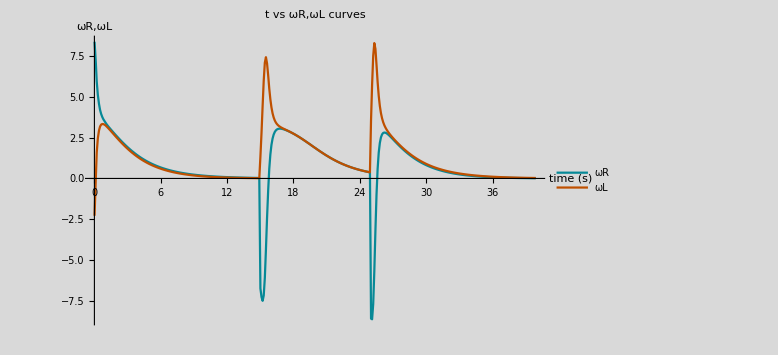

```mathematica
graf1=graphs1[{SampleVerify1,SampleVerify2},names3]
```

### 2.1.4 - Verifing the time channel:

By calculating a derivative in the time signal, it is possible verify that the time signal constitutes a linear data set.

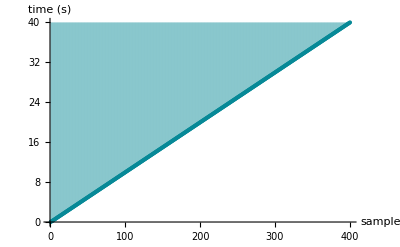

```mathematica
ListPlot[time,AxesLabel->{"sample","time (s)"}, Filling->Top]
```

Furthermore, by performing a more detailed analysis of time signal, it is possible to concluded that of the time signal evolves linearly due to the sampling frequency, possibly.

To calculate of the time interval Δt, it is calculated by subtracting of t(n+1) and t(n).

So,

Δt = t[[n+1]] - t[[n]]

The mean time interval Δtmean is defined by the calculate of the mean time interval. So:

```mathematica
tMeanDataSet =Table[Δt[n],{n,2,Length[time]}];
```

```mathematica
ΔtMean=Mean[tMeanDataSet];
```

where the “AverRefTimeInterval” is the average reference time interval.

```mathematica
AverRefTimeInterval=Table[ΔtMean ,{Length[tMeanDataSet]}];
```

Plotting this results in the “GrafTimeVariation” graphics, occurs:

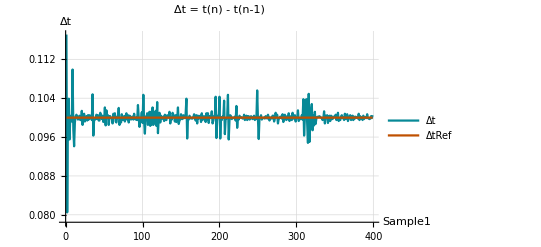

```mathematica
GrafTimeVariation=ListPlot[{tMeanDataSet,AverRefTimeInterval},Joined->True,PlotRange->All,GridLines->Automatic,AxesLabel->{"Sample1","Δt"},PlotLabel->"Δt = t(n) - t(n-1)", PlotLegends->Placed[{"Δt","ΔtRef"},{Right,Top}]]
```

## 2.2 - Calculating and verifying the “u” and “v” control signals:

### Prologue

Considering two wheels with r = rR = rL = 0,1 meters and the distance “d” between the wheels being 0,4 meters, and transfoming the velocity signals  “ωR” and “ωL” into control signals “u” and “ω”, it follows that:

uvelocity[n_, dataset_, ratio_] := ratio ((dataset[[1, n]] + dataset[[2, n]])/2)

ωvelocity[n_, dataset_, ratio_, distance_] := ratio ((dataset[[1, n]] - dataset[[2, n]])/distance)

The “u” and “ω” signals can be organizing in a “uωsignals” matrix. So:

```mathematica
{r,d,a}={0.1,0.4,0.1};
```

```mathematica
uωsignals=Transpose[Table[{uvelocity[n,{ωRigth,ωLeft},r],ωvelocity[n,{ωRigth,ωLeft},r,d]},{n,Length[time]}]];
```

```mathematica
Dimensions[uωsignals]
```

{2,400}

```mathematica
usignal=Transpose[{time,uωsignals[[1]]}]; 
usignal//Dimensions
ωsignal=Transpose[{time,uωsignals[[2]]}];
ωsignal//Dimensions
```

{400,2}

{400,2}

### Plotting the “time vs u” and “time vs ω” graphics, occurs:

graphs1[usignal, "u signal"]
graphs1[ωsignal, "ω signal"]

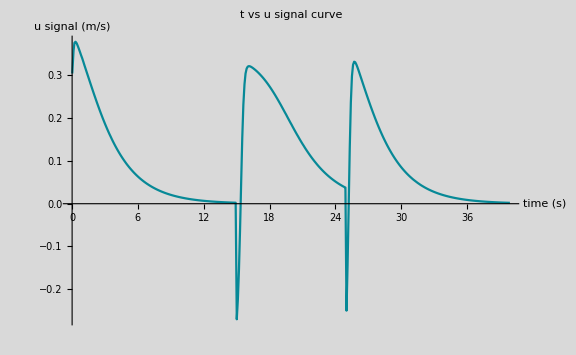

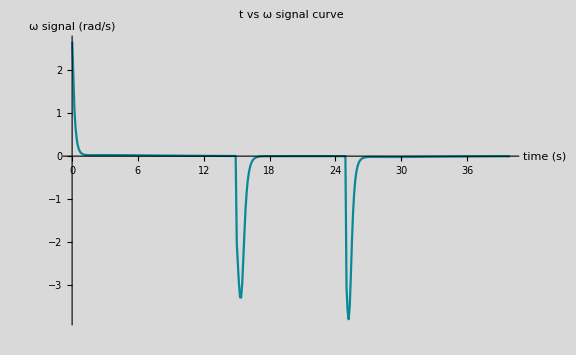

```mathematica
graphs2[usignal,"u signal","m/s"]
graphs2[ωsignal,"ω signal","rad/s"]
```

It is assumed that the robot starts from initial position (x0 , y0) = (0 , 0), with pose ψ0 = 0 rad.

## 2.3 - Orientation and Position:

### 2.3.1 - Orientation:

5. Use o modelo cinemático, para determinar a posição e orientação do robô ao longo do tempo. A título de exemplo, para determinar a orientação do robô, faça:

ψ̇(k) = [ψ(k) − ψ(k−1)]/Δt = ω ,

ou ainda:

ψ(k) = ψ(k−1) + ωΔt .

integrateFunctionRightRect[dataset,initalValues,interval]
integrateFunctionLeftRect[dataset,initalValues,interval]
integrateFunctionTrap[dataset,initalValues,interval]
IntEulerV13[dataset,initalValues]

```mathematica
ω=ωsignal;
```

```mathematica
ψSamples=ψv2[time,0][[All,2]];
```

```mathematica
ψSamples//Dimensions
```

{400}

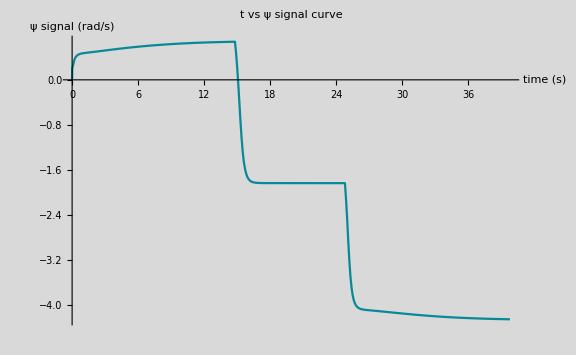

```mathematica
graphs2[ψv2[time,0],"ψ signal","rad/s"]
```

### 2.1.4 - Position:

#### The Dataset for calculations

```mathematica
(*globalveloc=globalvelocityv2[usignal[[All,2]],ωsignal[[All,2]],ψSamples,a];*)
```

##### i. The Global Velocities Dataset for calculations

```mathematica
globalvelocRigthRect=globalvelocityv2[usignal[[All,2]],ωsignal[[All,2]],integrateFunctionRightRect[ψpto,{0,0},"VI"][[All,2]],a];
```

```mathematica
globalvelocLeftRect=globalvelocityv2[usignal[[All,2]],ωsignal[[All,2]],integrateFunctionLeftRect[ψpto,{0,0},"VI"][[All,2]],a];
```

```mathematica
globalvelocTrap=globalvelocityv2[usignal[[All,2]],ωsignal[[All,2]],integrateFunctionTrap[ψpto,{0,0},"VI"][[All,2]],a];
```

```mathematica
globalvelocEuler=globalvelocityv2[usignal[[All,2]],ωsignal[[All,2]],IntEulerV13[ψpto,{0,0}][[All,2]],a];
```

##### ii. The Global Velocities Vectors for calculations

```mathematica
xpto=Transpose[{time,globalveloc[[All,1]]}];(* In function of "t" *)
ypto=Transpose[{time,globalveloc[[All,2]]}];(* In function of "t" *)
ψpto=Transpose[{time,globalveloc[[All,3]]}];(* In function of "t" *)
```

```mathematica
xptoRRect=Transpose[{time,globalvelocRigthRect[[All,1]]}];(* In function of "t" *)
yptoRRect=Transpose[{time,globalvelocRigthRect[[All,2]]}];(* In function of "t" *)
ψptoRRect=Transpose[{time,globalvelocRigthRect[[All,3]]}];(* In function of "t" *)
```

```mathematica
xptoLRect=Transpose[{time,globalvelocLeftRect[[All,1]]}];(* In function of "t" *)
yptoLRect=Transpose[{time,globalvelocLeftRect[[All,2]]}];(* In function of "t" *)
ψptoLRect=Transpose[{time,globalvelocLeftRect[[All,3]]}];(* In function of "t" *)
```

```mathematica
xptoTrap=Transpose[{time,globalvelocTrap[[All,1]]}];(* In function of "t" *)
yptoTrap=Transpose[{time,globalvelocTrap[[All,2]]}];(* In function of "t" *)
ψptoTrap=Transpose[{time,globalvelocTrap[[All,3]]}];(* In function of "t" *)
```

```mathematica
xptoEu=Transpose[{time,globalvelocEuler[[All,1]]}];(* In function of "t" *)
yptoEu=Transpose[{time,globalvelocEuler[[All,2]]}];(* In function of "t" *)
ψptoEu=Transpose[{time,globalvelocEuler[[All,3]]}];(* In function of "t" *)
```

#### a - Integrating by Right Rectangle Method

##### a.1 - Right Rectangle

```mathematica
(*xglobA1=integrateFunctionRightRect[xpto,{0,0},"VI"];
yglobA2=integrateFunctionRightRect[ypto,{0,0},"VI"];
ψglobA3=integrateFunctionRightRect[ψpto,{0,0},"VI"];
solBackRectMethod={time,xglobA1,yglobA2,ψglobA3};*)
```

```mathematica
xglobA1=integrateFunctionRightRect[xptoRRect,{0,0},"VI"];
yglobA2=integrateFunctionRightRect[yptoRRect,{0,0},"VI"];
ψglobA3=integrateFunctionRightRect[ψptoEu,{0,0},"VI"];
solBackRectMethod={time,xglobA1,yglobA2,ψglobA3};
```

##### a.2 - Right Rectangle Method Error

```mathematica
(*xglobErrorA4=OhErrorType1[xglobA1,"P"];
yglobErrorA5=OhErrorType1[yglobA2,"P"];
ψglobErrorA6=OhErrorType1[ψglobA3,"P"];
BackRectMethodError={xglobErrorA4,yglobErrorA5,ψglobErrorA6};*)
```

##### a.3 - Graphics

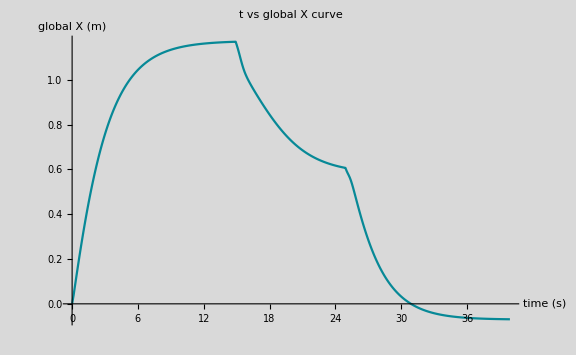

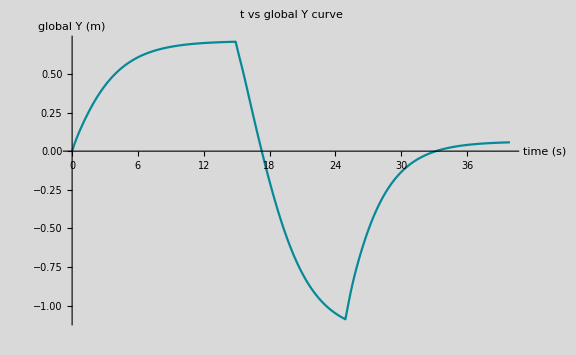

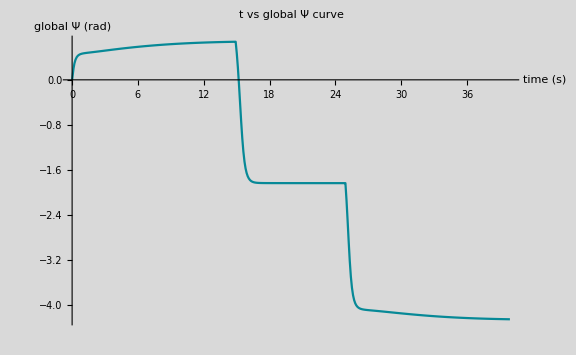

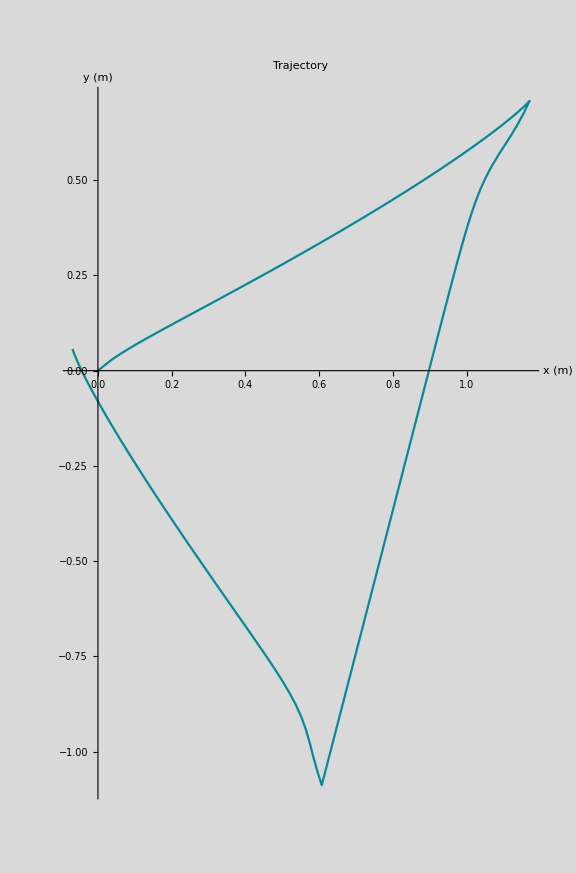

```mathematica
graf2=graphs2[xglobA1,"global X","m"]
graf3=graphs2[yglobA2,"global Y","m"]
graf4=graphs2[ψglobA3,"global Ψ","rad"]
graf5=graphs3[Transpose[{xglobA1[[All,2]],yglobA2[[All,2]]}],"Trajectory" ,{"x","y"},{"m","m"}]
```

#### b - Integrating by Center Point Method

##### b.1 - Center Point Method

```mathematica
(*xglobB7=integrateFunctionCentPtRect[xpto,"VI"];
yglobB8=integrateFunctionCentPtRect[ypto,"VI"];
ψglobB9=integrateFunctionCentPtRect[ψpto,"VI"];
solCentPtMethod={time,xglobB7,yglobB8,ψglobB9};*)
```

##### b.2 - Center Point Method Error

```mathematica
(*xglobErrorB10=OhErrorType2[xglobB7,"P"];
yglobErrorB11=OhErrorType2[yglobB8,"P"];
ψglobErrorB12=OhErrorType2[ψglobB9,"P"];
CentPtMethodError={xglobErrorB10,yglobErrorB11,ψglobErrorB12};*)
```

##### b.3 - Graphics

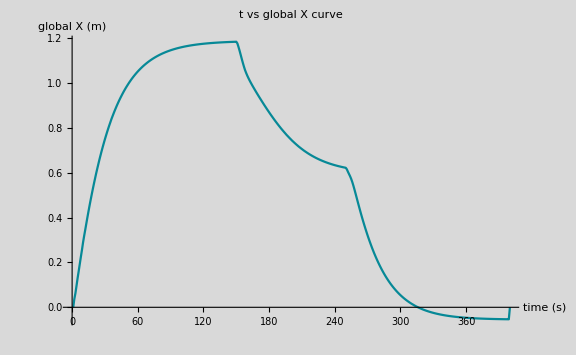

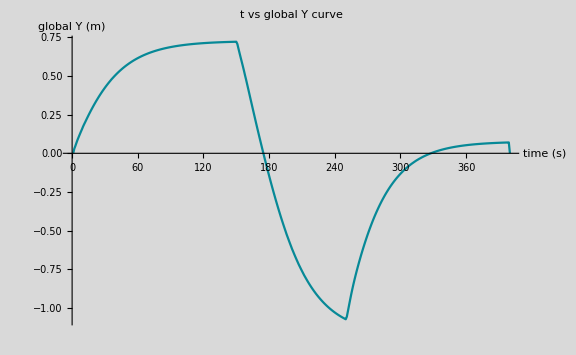

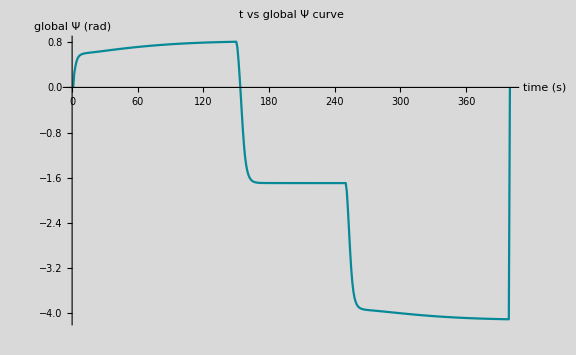

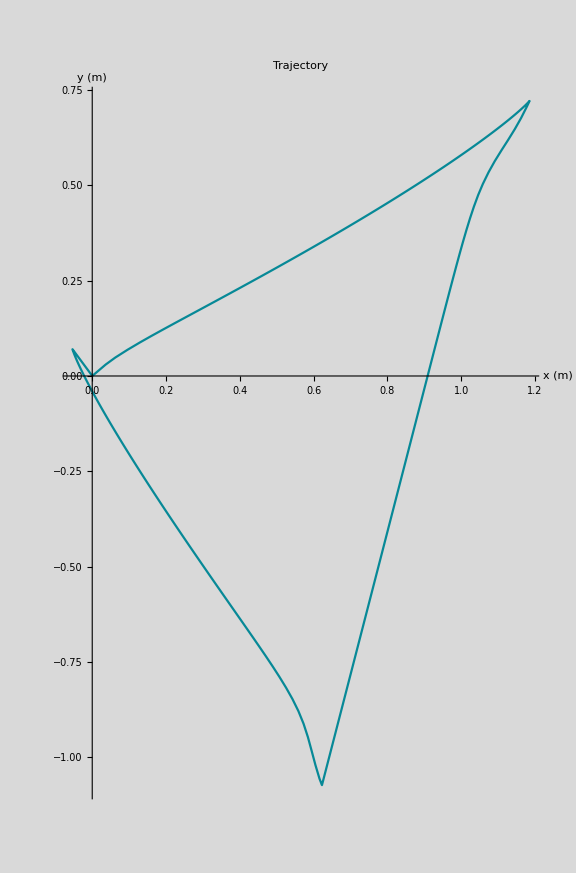

```mathematica
(*graf6=graphs2[xglobB7,"global X","m"]
graf7=graphs2[yglobB8,"global Y","m"]
graf8=graphs2[ψglobB9,"global Ψ","rad"]
graf9=graphs3[Transpose[{xglobB7,yglobB8}],"Trajectory" ,{"x","y"},{"m","m"}]*)
```

#### c - Integrating by Left Rectangle Method

##### c.1 - Left Rectangle

```mathematica
(*xglobC13=integrateFunctionLeftRect[xpto,{0,0},"VI"];
yglobC14=integrateFunctionLeftRect[ypto,{0,0},"VI"];
ψglobC15=integrateFunctionLeftRect[ψpto,{0,0},"VI"];
solRectForwMethod={time,xglobC13,yglobC14,ψglobC15};*)
```

GraphicsGrid[{{graf2, gjy}, {gy1, gjy}}]

GraphicsGrid[{{graf3, gjy}, {gy1, gjy}}]

GraphicsGrid[{{graf4, gjy}, {gy1, gjy}}]

```mathematica
xglobC13=integrateFunctionLeftRect[xptoLRect,{0,0},"VI"];
yglobC14=integrateFunctionLeftRect[yptoLRect,{0,0},"VI"];
ψglobC15=integrateFunctionLeftRect[ψptoLRect,{0,0},"VI"];
solRectForwMethod={time,xglobC13,yglobC14,ψglobC15};
```

##### c.2 - Left Rectangle Method Error

```mathematica
(*xglobErrorC16=OhErrorType1[xglobC13,"P"];
yglobErrorC17=OhErrorType1[yglobC14,"P"];
ψglobErrorC18=OhErrorType1[ψglobC15,"P"];
ForwRectMethodError={xglobErrorC16,yglobErrorC17,ψglobErrorC18};*)
```

##### c.3 - Graphics

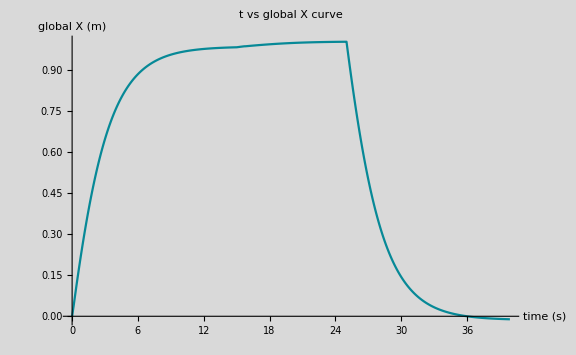

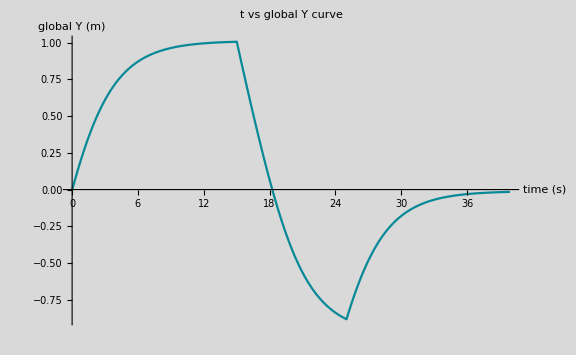

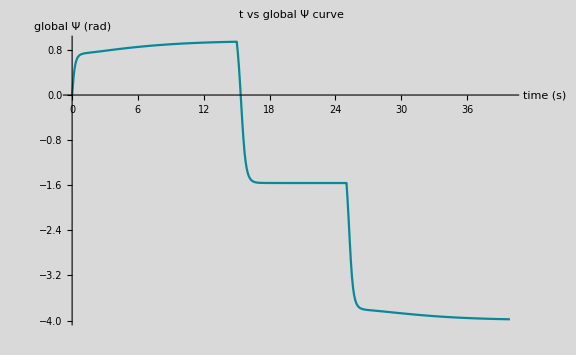

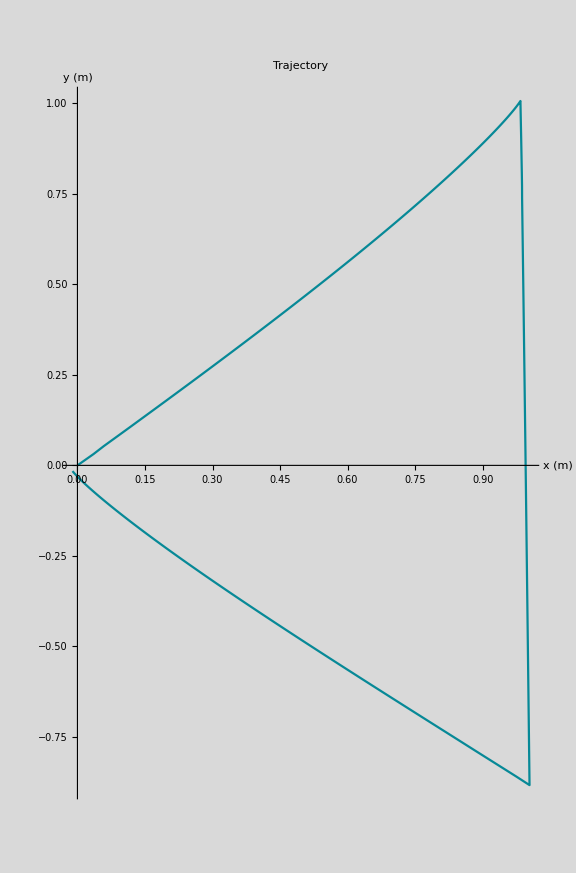

```mathematica
graf10=graphs2[xglobC13,"global X","m"]
graf11=graphs2[yglobC14,"global Y","m"]
graf12=graphs2[ψglobC15,"global Ψ","rad"]
graf13=graphs3[Transpose[{xglobC13[[All,2]],yglobC14[[All,2]]}],"Trajectory" ,{"x","y"},{"m","m"}]
```

#### d - Integrating by Trapezoidal Method

##### d.1 - Trapezoidal Method

```mathematica
(*xglobD19=integrateFunctionTrap[xpto,{0,0},"VI"];
yglobD20=integrateFunctionTrap[ypto,{0,0},"VI"];
ψglobD21=integrateFunctionTrap[ψpto,{0,0},"VI"];
solBackTrapMethod={time,xglobD19,yglobD20,ψglobD21};*)
```

```mathematica
xglobD19=integrateFunctionTrap[xptoTrap,{0,0},"VI"];
yglobD20=integrateFunctionTrap[yptoTrap,{0,0},"VI"];
ψglobD21=integrateFunctionTrap[ψptoTrap,{0,0},"VI"];
solBackTrapMethod={time,xglobD19,yglobD20,ψglobD21};
```

##### d.2 - Trapezoidal Method Error

```mathematica
(*xglobErrorD22=OhErrorType3[xpto,"P"];
yglobErrorD23=OhErrorType3[ypto,"P"];
ψglobErrorD24=OhErrorType3[ψpto,"P"];
BackTrapMethodError={xglobErrorD22,yglobErrorD23,ψglobErrorD24};*)
```

##### d.3 - Graphics

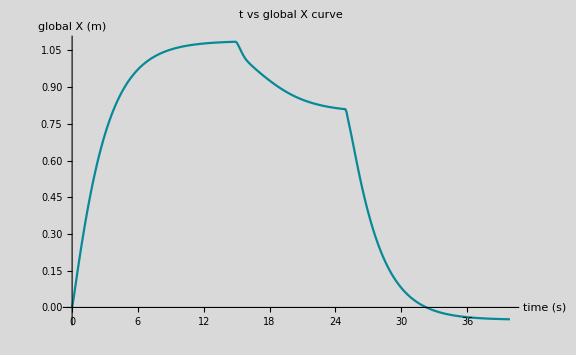

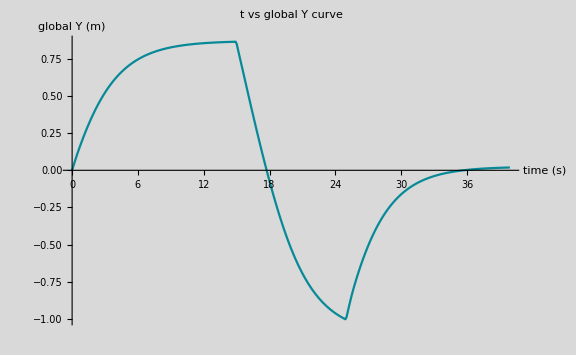

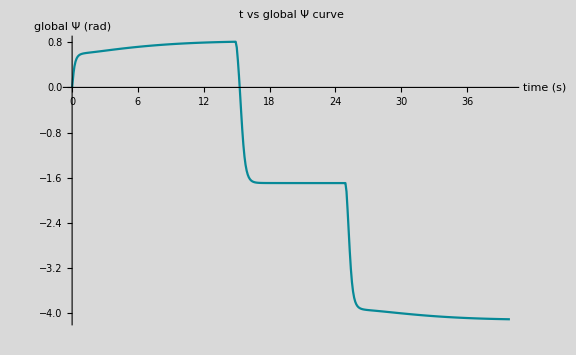

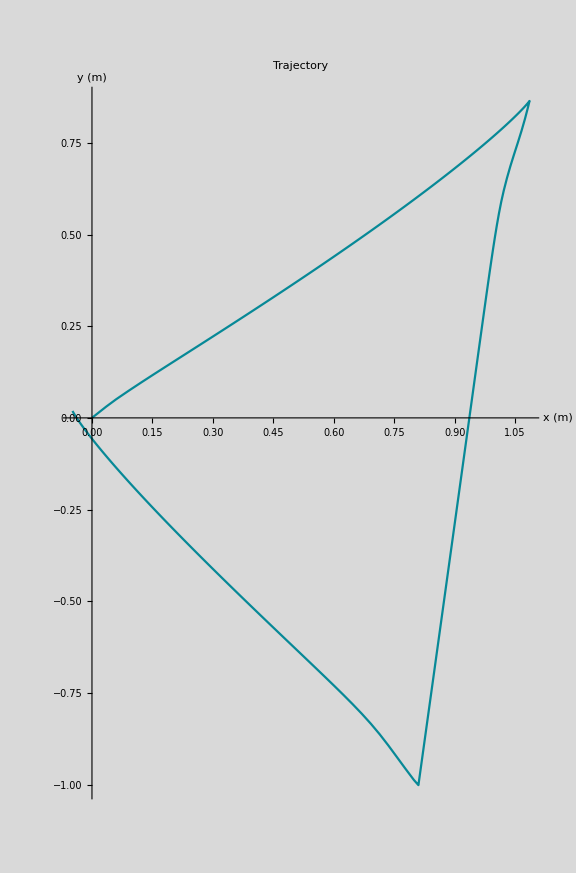

```mathematica
graf14=graphs2[xglobD19,"global X","m"]
graf15=graphs2[yglobD20,"global Y","m"]
graf16=graphs2[ψglobD21,"global Ψ","rad"]
graf17=graphs3[Transpose[{xglobD19[[All,2]],yglobD20[[All,2]]}],"Trajectory" ,{"x","y"},{"m","m"}]
```

#### d - Integrating by NONONO Trapezoidal Method

##### d.1 - Forward Trapezoidal Method

```mathematica
(*xglobE25=integrateFunctionForwTrap[xpto,"VI"];
yglobE26=integrateFunctionForwTrap[ypto,"VI"];
ψglobE27=integrateFunctionForwTrap[ψpto,"VI"];
solForwTrapMethod={time,xglobE25,yglobE26,ψglobE27};*)
```

##### d.2 - Forward Trapezoidal Method Error

```mathematica
(*xglobErrorE28=OhErrorType3[xglobE25,"P"];
yglobErrorE29=OhErrorType3[yglobE26,"P"];
ψglobErrorE30=OhErrorType3[ψglobE27,"P"];
ForwTrapMethodError={xglobErrorE28,yglobErrorE29,ψglobErrorE30};*)
```

##### e.3 - Graphics

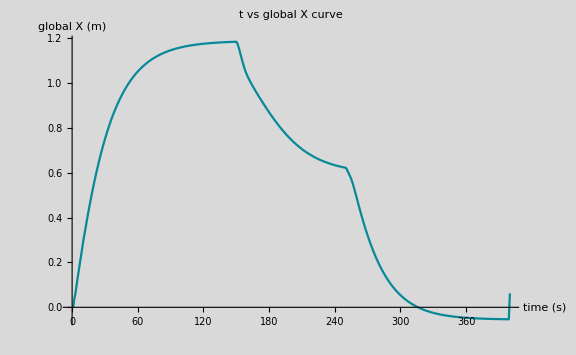

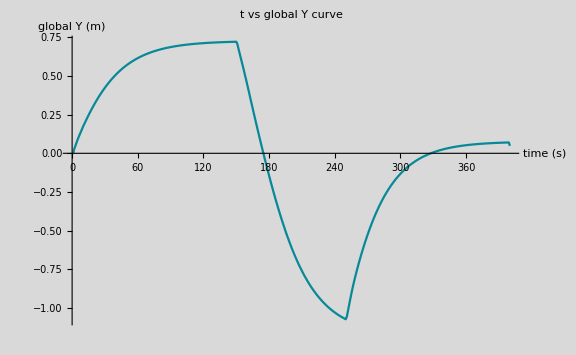

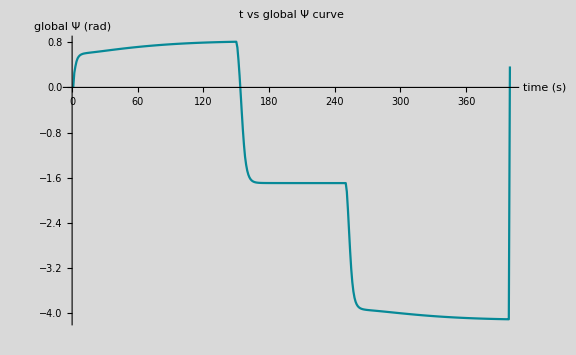

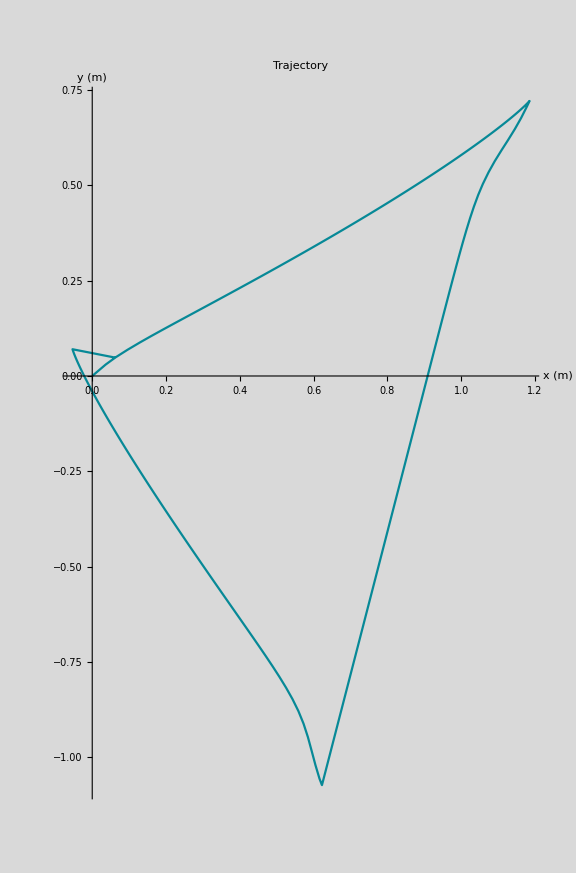

```mathematica
(*graf18=graphs2[xglobE25,"global X","m"]
graf19=graphs2[yglobE26,"global Y","m"]
graf20=graphs2[ψglobE27,"global Ψ","rad"]
graf21=graphs3[Transpose[{xglobE25,yglobE26}],"Trajectory" ,{"x","y"},{"m","m"}]*)
```

#### e - Integrating by Euler Method (Problem of Initial Value)

##### e.1 - Euler Method

```mathematica
(*xglobF31=IntEulerV13[xpto,{0,0}];
yglobF32=IntEulerV13[ypto,{0,0}];
ψglobF33=IntEulerV13[ψpto,{0,0}];
solEulerMethod={time,xglobF31,yglobF32,ψglobF33};*)
```

```mathematica
xglobF31=IntEulerV13[xptoEu,{0,0}];
yglobF32=IntEulerV13[yptoEu,{0,0}];
ψglobF33=IntEulerV13[ψptoEu,{0,0}];
solEulerMethod={time,xglobF31,yglobF32,ψglobF33};
```

##### e.2 - Euler Method Error

```mathematica
(*xglobErrorF34=OhErrorType1[xglobF31,"P"];
yglobErrorF35=OhErrorType1[yglobF32,"P"];
ψglobErrorF36=OhErrorType1[ψglobF33,"P"];
EulerMethodError={xglobErrorF34,yglobErrorF35,ψglobErrorF36};*)
```

##### e.3 - Graphics

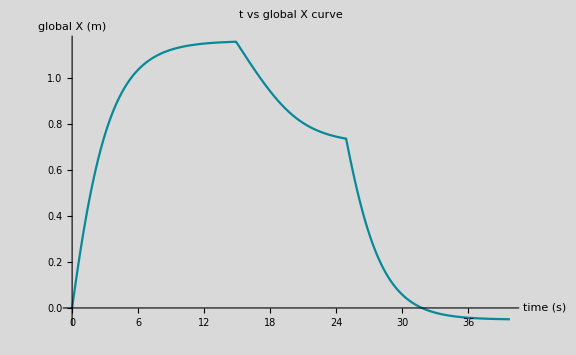

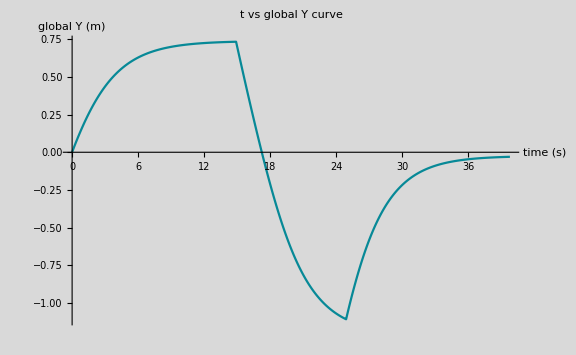

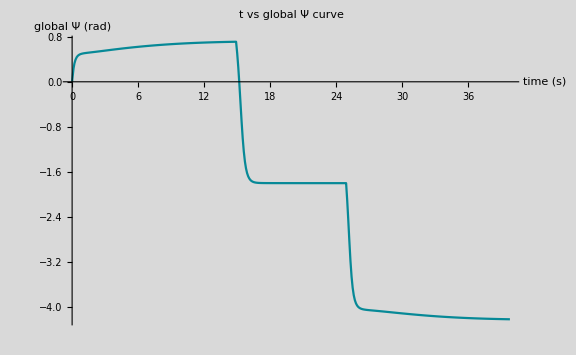

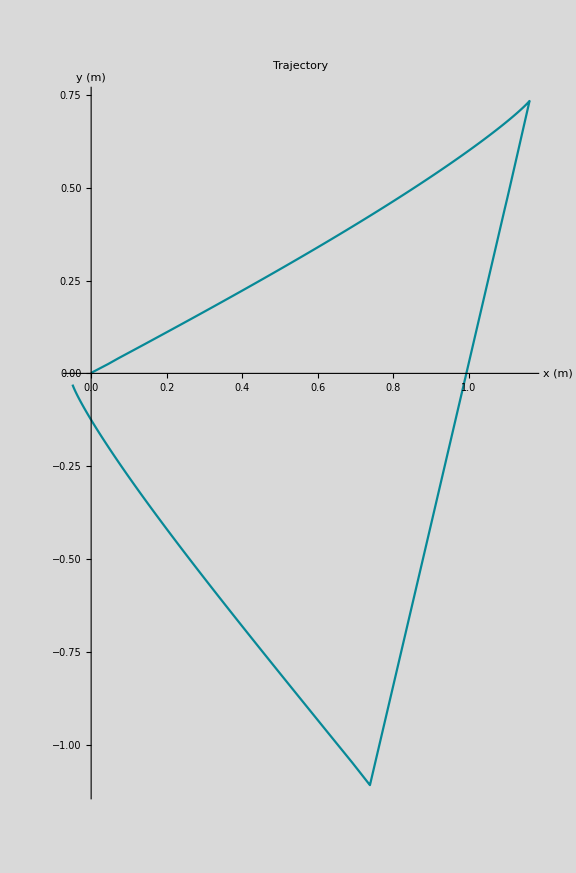

```mathematica
graf18=graphs2[xglobF31,"global X","m"]
graf19=graphs2[yglobF32,"global Y","m"]
graf20=graphs2[ψglobF33,"global Ψ","rad"]
graf21=graphs3[Transpose[{xglobF31[[All,2]],yglobF32[[All,2]]}],"Trajectory" ,{"x","y"},{"m","m"}]
```

```mathematica
??Show
```

tutorial/GraphicsAndSound#9501

### 2.1.4 - Results:

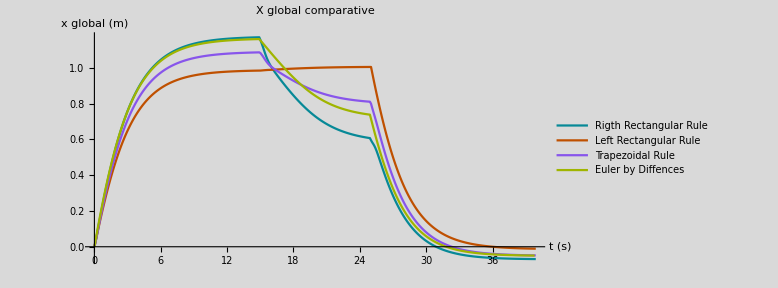

```mathematica
grafXglobal = graphs5[{xglobA1,xglobC13,xglobD19,xglobF31}, "X global comparative"  ,{"Rigth Rectangular Rule","Left Rectangular Rule","Trapezoidal Rule","Euler by Diffences"}, { "t","x global"}, {"s", "m"}]
```

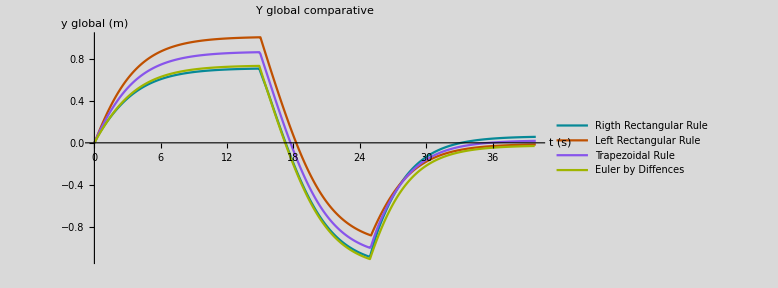

```mathematica
grafYglobal = graphs5[{yglobA2,yglobC14,yglobD20,yglobF32}, "Y global comparative"  ,{"Rigth Rectangular Rule","Left Rectangular Rule","Trapezoidal Rule","Euler by Diffences"}, { "t","y global"}, {"s", "m"}]
```

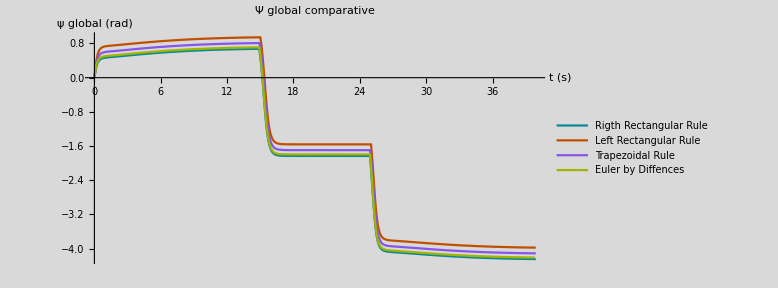

```mathematica
grafPSIglobal = graphs5[{ψglobA3,ψglobC15,ψglobD21,ψglobF33}, "Ψ global comparative"  ,{"Rigth Rectangular Rule","Left Rectangular Rule","Trapezoidal Rule","Euler by Diffences"}, { "t","ψ global"}, {"s", "rad"}]
```

```mathematica
{traj1,traj2,traj3,traj4}={Transpose[{xglobA1[[All, 2]], yglobA2[[All, 2]]}],Transpose[{xglobC13[[All, 2]], yglobC14[[All, 2]]}],Transpose[{xglobD19[[All, 2]], yglobD20[[All, 2]]}],Transpose[{xglobF31[[All, 2]], yglobF32[[All, 2]]}]};
```

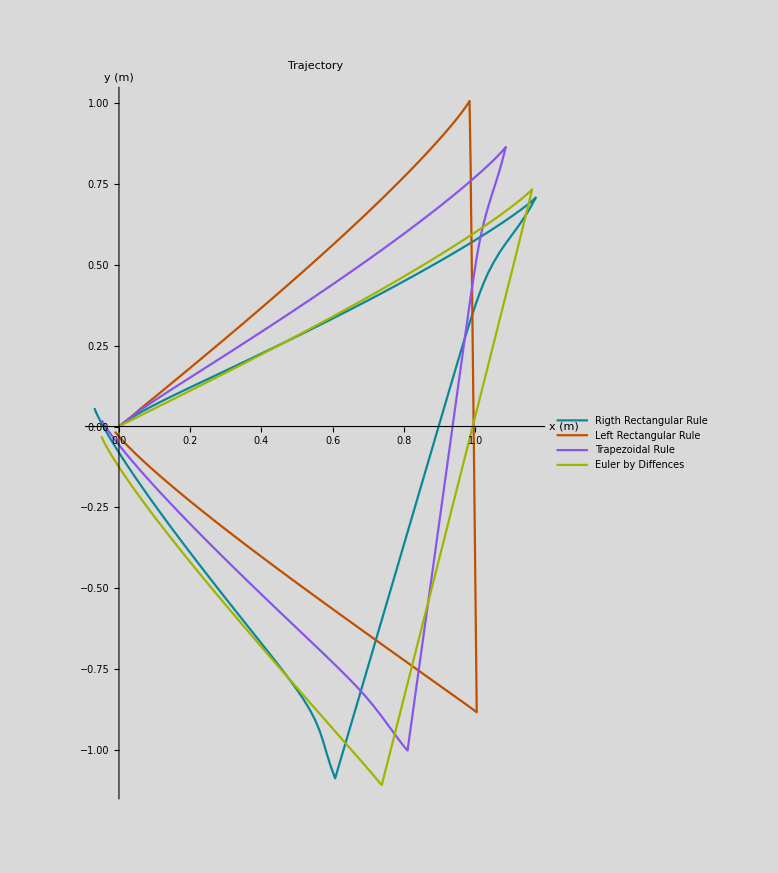

```mathematica
grafTrajectory = graphs4[{traj1,traj2,traj3,traj4}, "Trajectory" ,{"Rigth Rectangular Rule","Left Rectangular Rule","Trapezoidal Rule","Euler by Diffences"}, {"x", "y"}, {"m", "m"}]
```